Frequency: {{1,γ/(1-γ),0,0,0},{1,0,γ,γ^2/(1-γ),0},{1,0,γ,0,γ^2/(1-γ)}}

Measure: {(3-γ)/6,(3+γ)/12,(3+γ)/12}

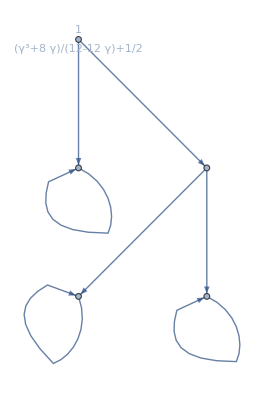

```mathematica
(*1*)

maxK = 4;
(*
For[k = 2, k≤  maxK, k++,
vertexAndNodes1 = {1->2 ,2->2,1->3};
If[k ==2,
vertexAndNodes1 = {1->2 ,2->2,1->3, 3->3};
, (*Else, k>2*)
For[i = 3, i<=k, i++,
AppendTo[vertexAndNodes1, i->i+1];
If[i ==k,
AppendTo[vertexAndNodes1, i+1->3];
,
];
];
];
fin = powerOfGraph[vertexAndNodes1, "First", "Measure"];
Print[fin];
];
*)

maxK = 4;
(*
For[k = 2, k≤  maxK, k++,
(*2*)

vertexAndNodes2 = {}; 
For[i = 1, i<=k, i++,
AppendTo[vertexAndNodes2, i->i+1];
If[i ==k,
AppendTo[vertexAndNodes2, 1->i+1];
AppendTo[vertexAndNodes2, i+1->i+1];
,
];
];
(*
powerOfGraph[vertexAndNodes2, "First", "Basic"]
*)
fin = powerOfGraph[vertexAndNodes2, "First", "Measure"];
Print[fin];
];
*)
(*3*)
vertexAndNodes3 = {1->2, 2->3, 1->3, 3->4, 4->4, 2->5, 5->5};
vertexAndNodes3 = {1->2,2->1, 2->2, 1->3, 3->4, 4->4};
vertexAndNodes3 = {1->1, 1->2, 2->3, 3->2, 1->3};


(*4*)
vertexAndNodes4 = {1->2, 2->2, 1->3, 3->4, 4->4, 3->5, 5->5};
(*
powerOfGraph[vertexAndNodes4, "First", "Measure"]
*)
(*5*)
vertexAndNodes5 = {1->2, 1->3, 1->4, 2->1, 2->3, 2->4, 3->1, 3->2, 3->4, 4->1, 4->2, 4->3};
vertexAndNodes5 = {1->2, 1->3, 2->1, 2->3,3->1, 3->2};
```